```mathematica
DSolve[{A'[t]==-A[t]/τa,B'[t]==A[t]/τa-B[t]/τb,B[0]==0},{A[t],B[t]},t]
```

{{A[t]→ⅇ^(-t/τa) C[1],B[t]→(ⅇ^(-t/τa-t/τb) (-ⅇ^(t/τa)+ⅇ^(t/τb)) τb C[1])/(τa-τb)}}

```mathematica
A[t_]:=ⅇ^(-t/τa)(10000) 
B[t_]:=(ⅇ^(-t/τa-t/τb) (-ⅇ^(t/τa)+ⅇ^(t/τb)) τb(10000))/(τa-τb)
τa=10;τb=5;
```

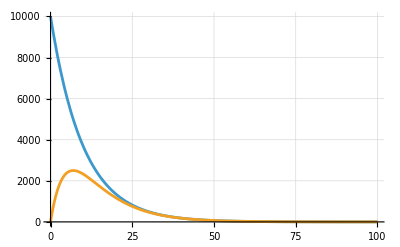

```mathematica
Plot[{A[t],B[t]},{t,0,100},PlotRange->{{0,100},{0,10000}},GridLines->Automatic]
```